# IPPT Model

## 3d. Multiple-Set Data Import (4)

Description:
- This notebook will import the results from “3b. Multiple-Pulse Data Export” for any propellant choice using four input files.
- Results are imported from WDX format from desired file path on PC.

How to Run:
- First, evaluate notebooks 1 and 2b for propellant of choice. Export data using 3b to create a WDX file type.
- Pull the desired three files to “Documents” folder on PC, or to whichever folder Mathematica is auto-tethered.
- Either click “Evaluate Notebook” in Menu Options or import file manually.

## Data Import

Notes:
- Adjust the date the files were produced and the shot numbers to reflect desired data sources

```mathematica
Filedate1 = "2021-09-07";
Filedate2 = "2021-09-07";
Filedate3 = "2021-09-07";
Filedate4 = "2021-09-07";
Shotnum1 = "1"; 
Shotnum2 = "2";
Shotnum3 = "3";
Shotnum4 = "4";
Codeversion = "1.12";

snowplowBool = 0;

filename1 = StringJoin[Filedate1,"_v",Codeversion,"_run_",Shotnum1,".wdx"];
shotdata1 = Import[filename1];
filename2 = StringJoin[Filedate2,"_v",Codeversion,"_run_",Shotnum2,".wdx"];
shotdata2 = Import[filename2];
filename3 = StringJoin[Filedate3,"_v",Codeversion,"_run_",Shotnum3,".wdx"];
shotdata3 = Import[filename3];
filename4 = StringJoin[Filedate4,"_v",Codeversion,"_run_",Shotnum4,".wdx"];
shotdata4 = Import[filename4];
```

## Unpack Data

```mathematica
tmaxt1 = shotdata1[[3]];
tmaxt2 = shotdata2[[3]];
tmaxt3 = shotdata3[[3]];
tmaxt4 = shotdata4[[3]];

χi0t1=shotdata1[[7]];
Lct1=shotdata1[[13]];
L0t1=shotdata1[[14]];
C0t1=shotdata1[[16]];
zct1 = shotdata1[[18]];
χi0t2=shotdata2[[7]];
Lct2=shotdata2[[13]];
L0t2=shotdata2[[14]];
C0t2=shotdata2[[16]];
zct2 = shotdata2[[18]];
χi0t3=shotdata3[[7]];
Lct3=shotdata3[[13]];
L0t3=shotdata3[[14]];
C0t3=shotdata3[[16]];
zct3= shotdata3[[18]];
χi0t4=shotdata4[[7]];
Lct4=shotdata4[[13]];
L0t4=shotdata4[[14]];
C0t4=shotdata4[[16]];
zct4= shotdata4[[18]];

τLC1=N[2π(C0t1 Lct1)^(1/2)];
τLC2=N[2π(C0t2 Lct2)^(1/2)];
τLC3=N[2π(C0t3 Lct3)^(1/2)];
τLC4=N[2π(C0t4 Lct4)^(1/2)];

nn1=shotdata1[[24]];
ws1=shotdata1[[25]];
zs1=shotdata1[[26]];
vs1=shotdata1[[27]];
vf1=shotdata1[[28]];
ns1=shotdata1[[29]];
nf1=shotdata1[[30]];
Ic1=shotdata1[[31]];
Ip1=shotdata1[[32]];
M1=shotdata1[[33]];
V1=shotdata1[[34]];
Te1=shotdata1[[35]];
Ti1=shotdata1[[36]];
ps1=shotdata1[[37]];
KEs1=shotdata1[[38]];
Ef1=shotdata1[[39]];
mbit1=shotdata1[[40]];
ms1[t_]=shotdata1[[41]];
Epi1=shotdata1[[42]];
Eel1=shotdata1[[43]];
Eind1[t_]=shotdata1[[44]];
Ecap1[t_]=shotdata1[[45]];
Eke1[t_]=shotdata1[[46]];
EkePl1[t_]=shotdata1[[47]];
EkeEnt1[t_]=shotdata1[[48]];
Ete1[t_]=shotdata1[[49]];
Ibit1[t_]=shotdata1[[50]];
Isp1[t_]=shotdata1[[51]];
ηm1[t_]=shotdata1[[52]];
MassFrac1[t_]=shotdata1[[53]];
ηT1[t_]=shotdata1[[54]];
ηTrec1[t_]=shotdata1[[55]];
Πiont1[t_]=shotdata1[[56]];
Πiont21[t_]=shotdata1[[57]];
Πcext21[t_]=shotdata1[[58]];

nn2=shotdata2[[24]];
ws2=shotdata2[[25]];
zs2=shotdata2[[26]];
vs2=shotdata2[[27]];
vf2=shotdata2[[28]];
ns2=shotdata2[[29]];
nf2=shotdata2[[30]];
Ic2=shotdata2[[31]];
Ip2=shotdata2[[32]];
M2=shotdata2[[33]];
V2=shotdata2[[34]];
Te2=shotdata2[[35]];
Ti2=shotdata2[[36]];
ps2=shotdata2[[37]];
KEs2=shotdata2[[38]];
Ef2=shotdata2[[39]];
mbit2=shotdata2[[40]];
ms2[t_]=shotdata2[[41]];
Epi2=shotdata2[[42]];
Eel2=shotdata2[[43]];
Eind2[t_]=shotdata2[[44]];
Ecap2[t_]=shotdata2[[45]];
Eke2[t_]=shotdata2[[46]];
EkePl2[t_]=shotdata2[[47]];
EkeEnt2[t_]=shotdata2[[48]];
Ete2[t_]=shotdata2[[49]];
Ibit2[t_]=shotdata2[[50]];
Isp2[t_]=shotdata2[[51]];
ηm2[t_]=shotdata2[[52]];
MassFrac2[t_]=shotdata2[[53]];
ηT2[t_]=shotdata2[[54]];
ηTrec2[t_]=shotdata2[[55]];
Πiont2[t_]=shotdata2[[56]];
Πiont22[t_]=shotdata2[[57]];
Πcext22[t_]=shotdata2[[58]];

nn3=shotdata3[[24]];
ws3=shotdata3[[25]];
zs3=shotdata3[[26]];
vs3=shotdata3[[27]];
vf3=shotdata3[[28]];
ns3=shotdata3[[29]];
nf3=shotdata3[[30]];
Ic3=shotdata3[[31]];
Ip3=shotdata3[[32]];
M3=shotdata3[[33]];
V3=shotdata3[[34]];
Te3=shotdata3[[35]];
Ti3=shotdata3[[36]];
ps3=shotdata3[[37]];
KEs3=shotdata3[[38]];
Ef3=shotdata3[[39]];
mbit3=shotdata3[[40]];
ms3[t_]=shotdata3[[41]];
Epi3=shotdata3[[42]];
Eel3=shotdata3[[43]];
Eind3[t_]=shotdata3[[44]];
Ecap3[t_]=shotdata3[[45]];
Eke3[t_]=shotdata3[[46]];
EkePl3[t_]=shotdata3[[47]];
EkeEnt3[t_]=shotdata3[[48]];
Ete3[t_]=shotdata3[[49]];
Ibit3[t_]=shotdata3[[50]];
Isp3[t_]=shotdata3[[51]];
ηm3[t_]=shotdata3[[52]];
MassFrac3[t_]=shotdata3[[53]];
ηT3[t_]=shotdata3[[54]];
ηTrec3[t_]=shotdata3[[55]];
Πiont3[t_]=shotdata3[[56]];
Πiont23[t_]=shotdata3[[57]];
Πcext23[t_]=shotdata3[[58]];

If[snowplowBool==0,
nn4=shotdata4[[24]];
ws4=shotdata4[[25]];
zs4=shotdata4[[26]];
vs4=shotdata4[[27]];
vf4=shotdata4[[28]];
ns4=shotdata4[[29]];
nf4=shotdata4[[30]];
Ic4=shotdata4[[31]];
Ip4=shotdata4[[32]];
M4=shotdata4[[33]];
V4=shotdata4[[34]];
Te4=shotdata4[[35]];
Ti4=shotdata4[[36]];
ps4=shotdata4[[37]];
KEs4=shotdata4[[38]];
Ef4=shotdata4[[39]];
mbit4=shotdata4[[40]];
ms4[t_]=shotdata4[[41]];
Epi4=shotdata4[[42]];
Eel4=shotdata4[[43]];
Eind4[t_]=shotdata4[[44]];
Ecap4[t_]=shotdata4[[45]];
Eke4[t_]=shotdata4[[46]];
EkePl4[t_]=shotdata4[[47]];
EkeEnt4[t_]=shotdata4[[48]];
Ete4[t_]=shotdata4[[49]];
Ibit4[t_]=shotdata4[[50]];
Isp4[t_]=shotdata4[[51]];
ηm4[t_]=shotdata4[[52]];
MassFrac4[t_]=shotdata4[[53]];
ηT4[t_]=shotdata4[[54]];
ηTrec4[t_]=shotdata4[[55]];
Πiont4[t_]=shotdata4[[56]];
Πiont24[t_]=shotdata4[[57]];
Πcext24[t_]=shotdata4[[58]];
,
nn4[z_,t_]=shotdata4[[24]];
ws4[t_]=shotdata4[[25]];
zs4[t_]=shotdata4[[26]];
vs4[t_]=shotdata4[[27]];
vf4[t_]=shotdata4[[28]];
ns4[t_]=shotdata4[[29]];
nf4[t_]=shotdata4[[30]];
Ic4[t_]=shotdata4[[31]];
Ip4[t_]=shotdata4[[32]];
M4[t_]=shotdata4[[33]];
V4[t_]=shotdata4[[34]];
Te4[t_]=shotdata4[[35]];
Ti4[t_]=shotdata4[[36]];
ps4[t_]=shotdata4[[37]];
KEs4[t_]=shotdata4[[38]];
Ef4[t_]=shotdata4[[39]];
mbit4=shotdata4[[40]];
ms4[t_]=shotdata4[[41]];
Epi4=shotdata4[[42]];
Eel4=shotdata4[[43]];
Eind4[t_]=shotdata4[[44]];
Ecap4[t_]=shotdata4[[45]];
Eke4[t_]=shotdata4[[46]];
EkePl4[t_]=shotdata4[[47]];
EkeEnt4[t_]=shotdata4[[48]];
Ete4[t_]=shotdata4[[49]];
Ibit4[t_]=shotdata4[[50]];
Isp4[t_]=shotdata4[[51]];
ηm4[t_]=shotdata4[[52]];
MassFrac4[t_]=shotdata4[[53]];
ηT4[t_]=shotdata4[[54]];
ηTrec4[t_]=shotdata4[[55]];
Πiont4[t_]=shotdata4[[56]];
Πiont24[t_]=shotdata4[[57]];
Πcext24[t_]=shotdata4[[58]];]

(* Calculate non-imported energy fraction *)
EnergyFrac1[t_]=(Eke1[t]+KEs1[t])/(Eel1+Epi1-Ecap1[t]);
EnergyFrac2[t_]=(Eke2[t]+KEs2[t])/(Eel2+Epi2-Ecap2[t]);
EnergyFrac3[t_]=(Eke3[t]+KEs3[t])/(Eel3+Epi3-Ecap3[t]);
EnergyFrac4[t_]=(Eke4[t]+KEs4[t])/(Eel4+Epi4-Ecap4[t]);
```

## Plot Styles

```mathematica
zcTimePlot[Fun1_,Fun2_,Fun3_,Fun4_,Plotlabel_,Axislabel_,tmax_,scale_]:=
Plot[{Fun1[t/10^6]scale,Fun2[t/10^6]scale,Fun3[t/10^6] scale,Fun4[t/10^6] scale},{t,0,10^6 tmax},
PlotRange->All,
Frame->True,
AspectRatio->1,
ImageSize->400,
PlotLabel-> StringJoin["Time-Evolution of ",Plotlabel],
FrameLabel->{"Time, t (μs)",Axislabel},
PlotLegends->{StringJoin[{"z_c = ",ToString[zct1]," m"}],StringJoin[{"z_c = ",ToString[zct2]," m"}],StringJoin[{"z_c = ",ToString[zct3]," m"}],StringJoin[{"z_c = ",ToString[zct4]," m"}]},
Axes->False,
LabelStyle->{16,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
piTimePlot[Fun1_,Fun2_,Fun3_,Fun4_,Plotlabel_,Axislabel_,tmax_,scale_]:=
Plot[{Fun1[t/10^6]scale,Fun2[t/10^6]scale,Fun3[t/10^6] scale,Fun4[t/10^6] scale},{t,0,10^6 tmax},
PlotRange->All,
Frame->True,
AspectRatio->1,
ImageSize->400,
PlotLabel-> StringJoin["Time-Evolution of ",Plotlabel],
FrameLabel->{"Time, t (μs)",Axislabel},
PlotLegends->{StringJoin[{"χ_0 = ",ToString[χi0t1]}],StringJoin[{"χ_0 = ",ToString[χi0t2]}],StringJoin[{"χ_0 = ",ToString[χi0t3]}],"Snowplow"},
Axes->False,
LabelStyle->{16,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
zcEffPlot[Fun1_,Fun2_,Fun3_,Fun4_,Plotlabel_,Axislabel_,tmax_,scale_]:=
Plot[{Fun1[t/10^6]scale,Fun2[t/10^6]scale,Fun3[t/10^6]scale,Fun4[t/10^6] scale},{t,0,10^6 tmax},
PlotRange->{{0,10^6 tmaxt},{0,100}},
Frame->True,
AspectRatio->1,
ImageSize->400,
PlotLabel-> StringJoin["Time-Evolution of ",Plotlabel],
FrameLabel->{"Time, t (μs)",Axislabel},
PlotLegends->{StringJoin[{"z_c = ",ToString[zct1]," m"}],StringJoin[{"z_c = ",ToString[zct2]," m"}],StringJoin[{"z_c = ",ToString[zct3]," m"}],StringJoin[{"z_c = ",ToString[zct4]," m"}]},
Axes->False,
LabelStyle->{16,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
piEffPlot[Fun1_,Fun2_,Fun3_,Fun4_,Plotlabel_,Axislabel_,tmax_,scale_]:=
Plot[{Fun1[t/10^6]scale,Fun2[t/10^6]scale,Fun3[t/10^6]scale,Fun4[t/10^6] scale},{t,0,10^6 tmax},
PlotRange->{{0,10^6 tmaxt},{0,100}},
Frame->True,
AspectRatio->1,
ImageSize->400,
PlotLabel-> StringJoin["Time-Evolution of ",Plotlabel],
FrameLabel->{"Time, t (μs)",Axislabel},
PlotLegends->{StringJoin[{"χ_0 = ",ToString[χi0t1]}],StringJoin[{"χ_0 = ",ToString[χi0t2]}],StringJoin[{"χ_0 = ",ToString[χi0t3]}],"Snowplow"},
Axes->False,
LabelStyle->{16,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
```

## All Variable Output, Coupling Distance and PI

```mathematica
ec=1.60217662 10^-19; (* electron charge *)

(** Print ICs **)
Print["Coupling distance (data set 1) = ",zct1];
Print["Coupling distance (data set 2) = ",zct2];
Print["Coupling distance (data set 3) = ",zct3];
Print["Coupling distance (data set 4) = ",zct4];
Print["Pre-ionization fraction (data set 1) = ",χi0t1];
Print["Pre-ionization fraction (data set 2) = ",χi0t2];
Print["Pre-ionization fraction (data set 3) = ",χi0t3];
Print["Pre-ionization fraction (data set 4) = ",χi0t4];

(** Plot state properties **)
(* Neutral density is a function of both z and t *)
Print[zcTimePlot[ws1,ws2,ws3,ws4,"Sheet Width","w_s (m)",tmaxt,1]];
Print[piTimePlot[ws1,ws2,ws3,ws4,"Sheet Width","w_s (m)",tmaxt,1]];
Print[zcTimePlot[zs1,zs2,zs3,zs4,"Sheet Position","z_s (m)",tmaxt,1]];
Print[piTimePlot[zs1,zs2,zs3,zs4,"Sheet Position","z_s (m)",tmaxt,1]];
Print[zcTimePlot[vs1,vs2,vs3,vs4,"Sheet Velocity","v_s (km/s)",tmaxt,10^-3]];
Print[piTimePlot[vs1,vs2,vs3,vs4,"Sheet Velocity","v_s (km/s)",tmaxt,10^-3]];
Print[zcTimePlot[vf1,vf2,vf3,vf4,"Entrained Neutral Velocity","v_f (km/s)",tmaxt,10^-3]];
Print[piTimePlot[vf1,vf2,vf3,vf4,"Entrained Neutral Velocity","v_f (km/s)",tmaxt,10^-3]];
Print[zcTimePlot[ns1,ns2,ns3,ns4,"Sheet Density","n_s (m^-3)",tmaxt,1]];
Print[piTimePlot[ns1,ns2,ns3,ns4,"Sheet Density","n_s (m^-3)",tmaxt,1]];
Print[zcTimePlot[nf1,nf2,nf3,nf4,"Entrained Neutral Density","n_f (m^-3)",tmaxt,1]];
Print[piTimePlot[nf1,nf2,nf3,nf4,"Entrained Neutral Density","n_f (m^-3)",tmaxt,1]];
Print[zcTimePlot[Ic1,Ic2,Ic3,Ic4,"Coil Current","I_c (kA)",tmaxt,10^-3]];
Print[piTimePlot[Ic1,Ic2,Ic3,Ic4,"Coil Current","I_c (kA)",tmaxt,10^-3]];
Print[zcTimePlot[Ip1,Ip2,Ip3,Ip4,"Plasma Current","I_p (kA)",tmaxt,10^-3]];
Print[piTimePlot[Ip1,Ip2,Ip3,Ip4,"Plasma Current","I_p (kA)",tmaxt,10^-3]];
Print[zcTimePlot[M1,M2,M3,M4,"Mutual Inductance","M (nH)",tmaxt,10^9]];
Print[piTimePlot[M1,M2,M3,M4,"Mutual Inductance","M (nH)",tmaxt,10^9]];
Print[zcTimePlot[V1,V2,V3,V4,"Circuit Voltage","V_c (kV)",tmaxt,10^-3]];
Print[piTimePlot[V1,V2,V3,V4,"Circuit Voltage","V_c (kV)",tmaxt,10^-3]];
Print[zcTimePlot[Te1,Te2,Te3,Te4,"Electron Temperature","T_e (eV)",tmaxt,1]];
Print[piTimePlot[Te1,Te2,Te3,Te4,"Electron Temperature","T_e (eV)",tmaxt,1]];
Print[zcTimePlot[Ti1,Ti2,Ti3,Ti4,"Ion Temperature","T_i (eV)",tmaxt,1]];
Print[piTimePlot[Ti1,Ti2,Ti3,Ti4,"Ion Temperature","T_i (eV)",tmaxt,1]];
Print[zcTimePlot[ps1,ps2,ps3,ps4,"Slipped Neutral Momentum","p_s (µN•s)",tmaxt,10^6]];
Print[piTimePlot[ps1,ps2,ps3,ps4,"Slipped Neutral Momentum","p_s (µN•s)",tmaxt,10^6]];
Print[zcTimePlot[KEs1,KEs2,KEs3,KEs4,"Slipped Neutral Kinetic Energy","KE_s (J)",tmaxt,1]];
Print[piTimePlot[KEs1,KEs2,KEs3,KEs4,"Slipped Neutral Kinetic Energy","KE_s (J)",tmaxt,1]];
Print[zcTimePlot[Ef1,Ef2,Ef3,Ef4,"Entrained Neutral Ionization Energy","E_f (J)",tmaxt,1]];
Print[piTimePlot[Ef1,Ef2,Ef3,Ef4,"Entrained Neutral Ionization Energy","E_f (J)",tmaxt,1]];
Print[
Plot[{ec 10^-3 ns1[t/10^6]Te1[t/10^6],ec 10^-3 ns2[t/10^6]Te2[t/10^6], ec 10^-3 ns3[t/10^6]Te3[t/10^6],ec 10^-3 ns4[t/10^6] Te4[t/10^6]},{t,0,10^6 tmaxt},
PlotRange->All,
Frame->True,
ImageSize->400,
PlotLabel-> "Time-Evolution of Sheet Pressure",
FrameLabel->{"Time, t (μs)","p_s (kPa)"},
PlotLegends->{StringJoin[{"z_c = ",ToString[zct1]," m"}],StringJoin[{"z_c = ",ToString[zct2]," m"}],StringJoin[{"z_c = ",ToString[zct3]," m"}],"Slowplow"},
Axes->False,
LabelStyle->{16,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]
];
Print[
Plot[{ec 10^-3 ns1[t/10^6]Te1[t/10^6],ec 10^-3 ns2[t/10^6]Te2[t/10^6], ec 10^-3 ns3[t/10^6]Te3[t/10^6],ec 10^-3 ns4[t/10^6] Te4[t/10^6]},{t,0,10^6 tmaxt},
PlotRange->All,
Frame->True,
ImageSize->400,
PlotLabel-> "Time-Evolution of Sheet Pressure",
FrameLabel->{"Time, t (μs)","p_s (kPa)"},
PlotLegends->{StringJoin[{"χ_0 = ",ToString[χi0t1]}],StringJoin[{"χ_0 = ",ToString[χi0t2]}],StringJoin[{"χ_0 = ",ToString[χi0t3]}],"Snowplow"},
Axes->False,
LabelStyle->{16,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]
];

(** Plot performance metrics **)
Print[zcTimePlot[ms1,ms2,ms3,ms4,"Sheet Mass","m_s (kg)",tmaxt,1]];
Print[piTimePlot[ms1,ms2,ms3,ms4,"Sheet Mass","m_s (kg)",tmaxt,1]];
Print[zcTimePlot[Eind1,Eind2,Eind3,Eind4,"Inductor Energy","E_ind (J)",tmaxt,1]];
Print[piTimePlot[Eind1,Eind2,Eind3,Eind4,"Inductor Energy","E_ind (J)",tmaxt,1]];
Print[zcTimePlot[Ecap1,Ecap2,Ecap3,Ecap4,"Capacitor Energy","E_cap (J)",tmaxt,1]];
Print[piTimePlot[Ecap1,Ecap2,Ecap3,Ecap4,"Capacitor Energy","E_cap (J)",tmaxt,1]];
Print[zcTimePlot[Eke1,Eke2,Eke3,Eke4,"Total Kinetic Energy","Energy (J)",tmaxt,1]];
Print[piTimePlot[Eke1,Eke2,Eke3,Eke4,"Total Kinetic Energy","Energy (J)",tmaxt,1]];
Print[zcTimePlot[EkePl1,EkePl2,EkePl3,EkePl4,"Kinetic Energy in Plasma","Energy (J)",tmaxt,1]];
Print[piTimePlot[EkePl1,EkePl2,EkePl3,EkePl4,"Kinetic Energy in Plasma","Energy (J)",tmaxt,1]];
Print[zcTimePlot[EkeEnt1,EkeEnt2,EkeEnt3,EkeEnt4,"Kinetic Energy in Entrained Neutrals","Energy (J)",tmaxt,1]];
Print[piTimePlot[EkeEnt1,EkeEnt2,EkeEnt3,EkeEnt4,"Kinetic Energy in Entrained Neutrals","Energy (J)",tmaxt,1]];
Print[zcTimePlot[Ete1,Ete2,Ete3,Ete4,"Thermal Energy","Energy (J)",tmaxt,1]];
Print[piTimePlot[Ete1,Ete2,Ete3,Ete4,"Thermal Energy","Energy (J)",tmaxt,1]];
Print[zcTimePlot[Ibit1,Ibit2,Ibit3,Ibit4,"Impulse Bit","I_bit (N•s)",tmaxt,1]];
Print[piTimePlot[Ibit1,Ibit2,Ibit3,Ibit4,"Impulse Bit","I_bit (N•s)",tmaxt,1]];
Print[zcTimePlot[Isp1,Isp2,Isp3,Isp4,"Specific Impulse","I_sp (s)",tmaxt,1]];
Print[piTimePlot[Isp1,Isp2,Isp3,Isp4,"Specific Impulse","I_sp (s)",tmaxt,1]];
Print[zcTimePlot[MassFrac1,MassFrac2,MassFrac3,MassFrac4,"Fraction of Mass Bit in Sheet","Mass Fraction",tmaxt,1]];
Print[piTimePlot[MassFrac1,MassFrac2,MassFrac3,MassFrac4,"Fraction of Mass Bit in Sheet","Mass Fraction",tmaxt,1]];
Print[zcEffPlot[ηm1,ηm2,ηm3,ηm4,"Mass Utilization Efficiency","η_m (%)",tmaxt,10^2]];
Print[piEffPlot[ηm1,ηm2,ηm3,ηm4,"Mass Utilization Efficiency","η_m (%)",tmaxt,10^2]];
Print[zcEffPlot[ηT1,ηT2,ηT3,ηT4,"Thruster Efficiency","η_T no energy recovery (%)",tmaxt,10^2]];
Print[piEffPlot[ηT1,ηT2,ηT3,ηT4,"Thruster Efficiency","η_T no energy recovery (%)",tmaxt,10^2]];
Print[zcEffPlot[ηTrec1,ηTrec2,ηTrec3,ηTrec4,"Thruster Efficiency","η_T (%)",tmaxt,10^2]];
Print[piEffPlot[ηTrec1,ηTrec2,ηTrec3,ηTrec4,"Thruster Efficiency","η_T (%)",tmaxt,10^2]];
Print[zcTimePlot[Πiont1,Πiont2,Πiont3,Πiont4,"Πion (1)","Πion (1)",tmaxt,1]];
Print[piTimePlot[Πiont1,Πiont2,Πiont3,Πiont4,"Πion (1)","Πion (1)",tmaxt,1]];
Print[zcTimePlot[Πiont21,Πiont22,Πiont23,Πiont24,"Πion (2)","Πion (2)",tmaxt,1]];
Print[piTimePlot[Πiont21,Πiont22,Πiont23,Πiont24,"Πion (2)","Πion (2)",tmaxt,1]];
Print[zcTimePlot[Πcext21,Πcext22,Πcext23,Πcext24,"Πcex","Πcex",tmaxt,1]];
Print[piTimePlot[Πcext21,Πcext22,Πcext23,Πcext24,"Πcex","Πcex",tmaxt,1]];
```

## All Variable Output, Inductance Comparison, Rev 1

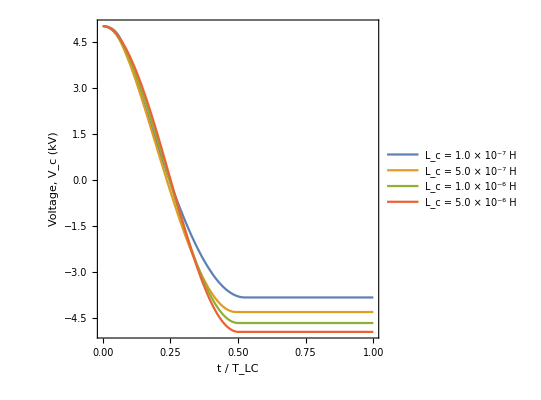

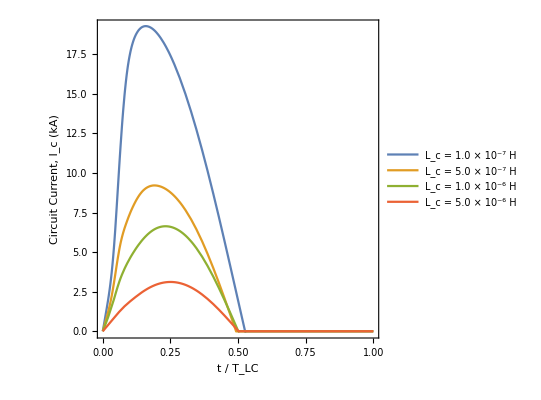

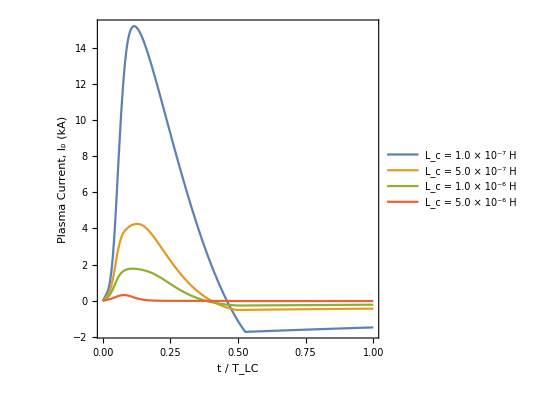

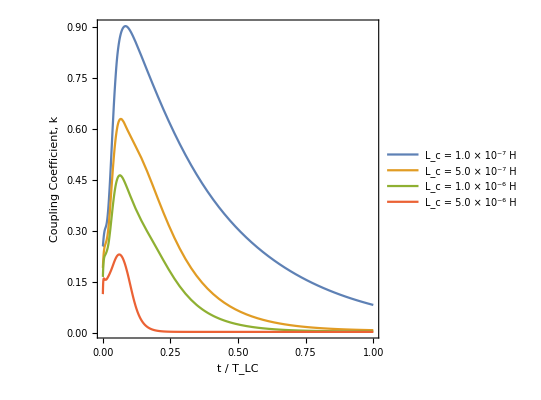

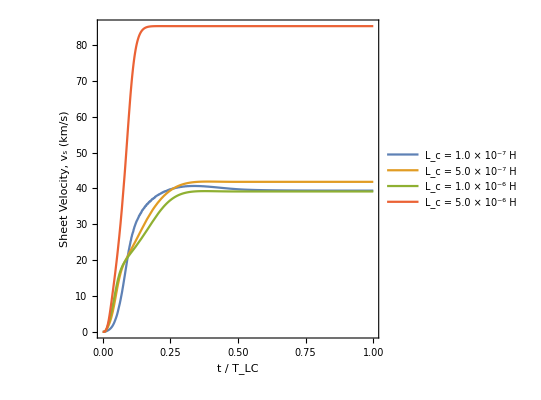

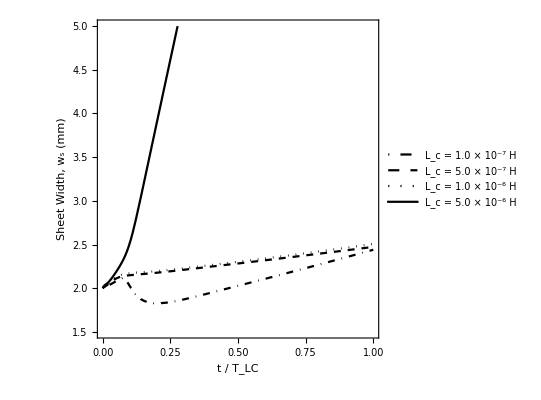

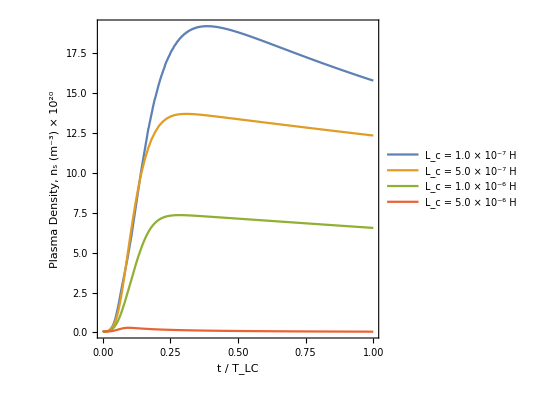

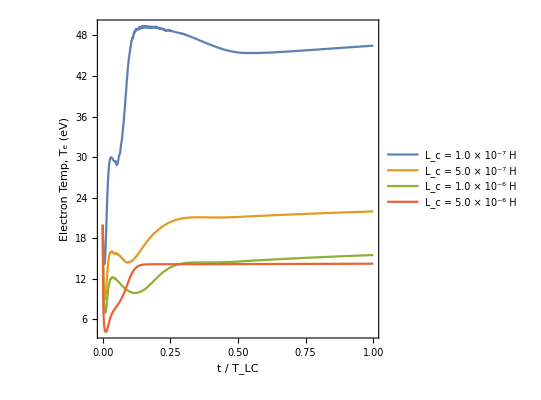

```mathematica
(** Adjust plot styles **)
LcPlot[Fun1_,Fun2_,Fun3_,Fun4_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale,Fun3[Τ τLC3]scale,Fun4[Τ τLC4]scale},{Τ,0,1},
PlotRange->{{0,1},All},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
PlotLegends->{"L_c = 1.0 × 10^-7 H","L_c = 5.0 × 10^-7 H","L_c = 1.0 × 10^-6 H","L_c = 5.0 × 10^-6 H"}, (* Hard-coded for JAP 9/21 *)
Axes->False,
LabelStyle->{18,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
EffLcPlot[Fun1_,Fun2_,Fun3_,Fun4_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale,Fun3[Τ τLC3] scale,Fun4[Τ τLC4] scale},{Τ,0,1},
PlotRange->{{0.02,1},{0,1}},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
PlotLegends->{"L_c = 1.0 × 10^-7 H","L_c = 5.0 × 10^-7 H","L_c = 1.0 × 10^-6 H","L_c = 5.0 × 10^-6 H"}, (* Hard-coded for JAP 9/21 *)
Axes->False,
LabelStyle->{18,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
JPlot[Fun1_,Fun2_,Fun3_,Fun4_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale,Fun3[Τ τLC3]scale,Fun4[Τ τLC4]scale},{Τ,0,1},
PlotRange->{{0,0.6},All},
(* PlotStyle->{{DotDashed,Black},{Dashed,Black},{Dotted,Black},{Black}}, *)
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
JkPlot[Fun1_,Fun2_,Fun3_,Fun4_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]/Lct1 scale,Fun2[Τ τLC2]/Lct2 scale,Fun3[Τ τLC3]/Lct3 scale,Fun4[Τ τLC4]/Lct4 scale},{Τ,0,1},
PlotRange->{{0,0.6},All},
(* PlotStyle->{{DotDashed,Black},{Dashed,Black},{Dotted,Black},{Black}}, *)
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
JwsPlot[Fun1_,Fun2_,Fun3_,Fun4_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1] scale,Fun2[Τ τLC2] scale,Fun3[Τ τLC3] scale,Fun4[Τ τLC4] scale},{Τ,0,1},
PlotRange->{{0,0.6},{1.5,5}},
(* PlotStyle->{{DotDashed,Black},{Dashed,Black},{Dotted,Black},{Black}}, *)
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
EffJPlot[Fun1_,Fun2_,Fun3_,Fun4_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale,Fun3[Τ τLC3]scale,Fun4[Τ τLC4]scale},{Τ,0,1},
PlotRange->{{0.02,0.6},{0,1}},
(* PlotStyle->{{DotDashed,Black},{Dashed,Black},{Dotted,Black},{Black}}, *)
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];

(** Individual Plots **)
LcPlot[V1,V2,V3,V4,"Voltage, V_c (kV)",10^-3]
LcPlot[Ic1,Ic2,Ic3,Ic4,"Circuit Current, I_c (kA)",10^-3]
LcPlot[Ip1,Ip2,Ip3,Ip4,"Plasma Current, I_p (kA)",10^-3]
Plot[{M1[Τ τLC1]/Lct1,M2[Τ τLC2]/Lct2,M3[Τ τLC3]/Lct3,M4[Τ τLC4]/Lct4},{Τ,0,1},
PlotRange->{{0,1},All},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC","Coupling Coefficient, k"},
PlotLegends->{"L_c = 1.0 × 10^-7 H","L_c = 5.0 × 10^-7 H","L_c = 1.0 × 10^-6 H","L_c = 5.0 × 10^-6 H"}, (* Hard-coded for JAP 9/21 *)
Axes->False,
LabelStyle->{18,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]
LcPlot[vs1,vs2,vs3,vs4,"Sheet Velocity, v_s (km/s)",10^-3]
Plot[{ws1[Τ τLC1] 10^3,ws2[Τ τLC2] 10^3,ws3[Τ τLC3] 10^3,ws4[Τ τLC4] 10^3},{Τ,0,1},
PlotRange->{{0,1},{1.5,5}},
PlotStyle->{{DotDashed,Black},{Dashed,Black},{Dotted,Black},{Black}},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC","Sheet Width, w_s (mm)"},
PlotLegends->{"L_c = 1.0 × 10^-7 H","L_c = 5.0 × 10^-7 H","L_c = 1.0 × 10^-6 H","L_c = 5.0 × 10^-6 H"}, (* Hard-coded for JAP 9/21 *)
Axes->False,
LabelStyle->{18,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]
LcPlot[ns1,ns2,ns3,ns4,"Plasma Density, n_s (m^-3) × 10^20",10^-20]
LcPlot[Te1,Te2,Te3,Te4,"Electron Temp, T_e (eV)",1]
LcPlot[Isp1,Isp2,Isp3,Isp4,"Specific Impulse, I_sp (ks)",10^-3]
EffLcPlot[ηm1,ηm2,ηm3,ηm4,"Mass Util. Eff., η_m",1]
LcPlot[EnergyFrac1,EnergyFrac2,EnergyFrac3,EnergyFrac4,"Electrical Eff., η_e",1]
LcPlot[ηTrec1,ηTrec2,ηTrec3,ηTrec4,"Thrust Efficiency, η_R",1]

(** Journal Output **)
Print[GraphicsGrid[{
{JPlot[V1,V2,V3,V4,"Voltage, V_c (kV)",10^-3],JPlot[Ic1,Ic2,Ic3,Ic4,"Circuit Current, I_c (kA)",10^-3],JPlot[Ip1,Ip2,Ip3,Ip4,"Plasma Current, I_p (kA)",10^-3],JkPlot[M1,M2,M3,M4,"Coupling Coefficient, k",1]},
{JPlot[vs1,vs2,vs3,vs4,"Sheet Velocity, v_s (km/s)",10^-3],JwsPlot[ws1,ws2,ws3,ws4,"Sheet Width, w_s (mm)",10^3],JPlot[ns1,ns2,ns3,ns4,"Plasma Density, n_s (m^-3) × 10^20",10^-20],JPlot[Te1,Te2,Te3,Te4,"Electron Temp, T_e (eV)",1]},
{JPlot[Isp1,Isp2,Isp3,Isp4,"Specific Impulse, I_sp (ks)",10^-3],EffJPlot[ηm1,ηm2,ηm3,ηm4,"Mass Util. Eff., η_m",1],JPlot[EnergyFrac1,EnergyFrac2,EnergyFrac3,EnergyFrac4,"Electrical Eff., η_e",1],JPlot[ηTrec1,ηTrec2,ηTrec3,ηTrec4,"Thrust Efficiency, η_R",1]}},
Spacings->{5,-5}, ImageSize-> 800]];
```

## All Variable Output, Snowplow Comparison, Rev 2

InterpolatingFunction::dmval: Input value {1.81524×10^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

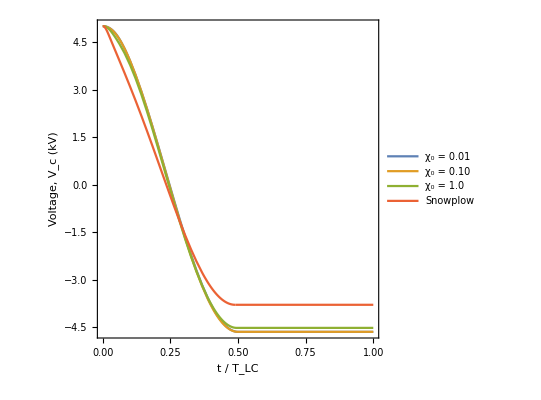

InterpolatingFunction::dmval: Input value {1.81524×10^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

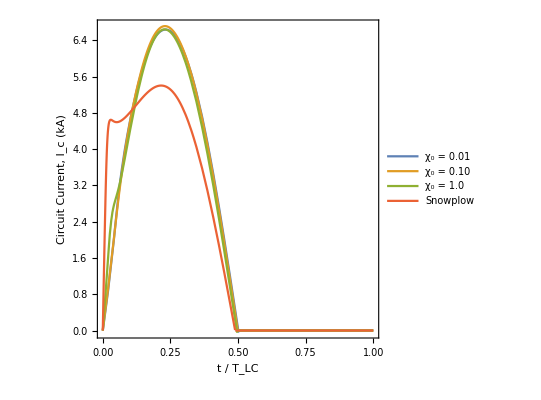

InterpolatingFunction::dmval: Input value {1.81524×10^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

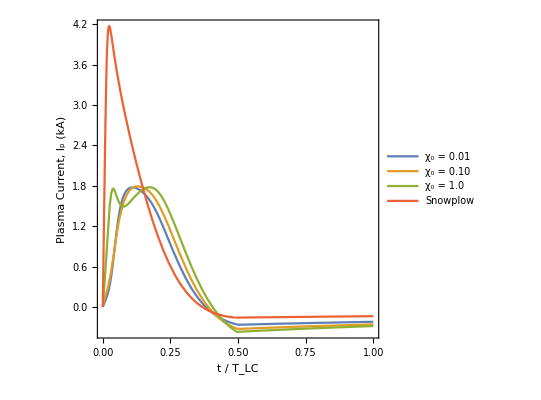

InterpolatingFunction::dmval: Input value {1.81524×10^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

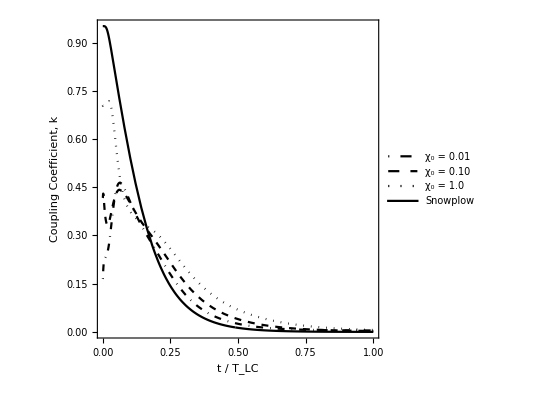

InterpolatingFunction::dmval: Input value {1.81524×10^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

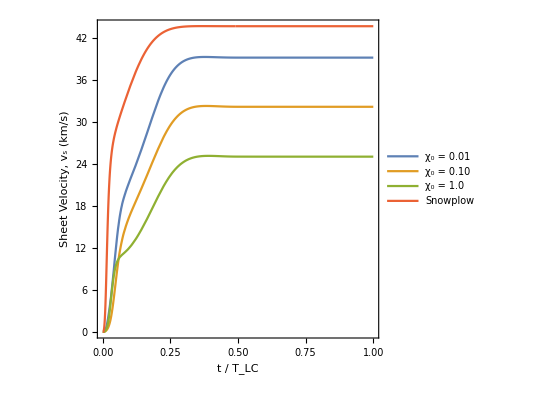

InterpolatingFunction::dmval: Input value {1.81524×10^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

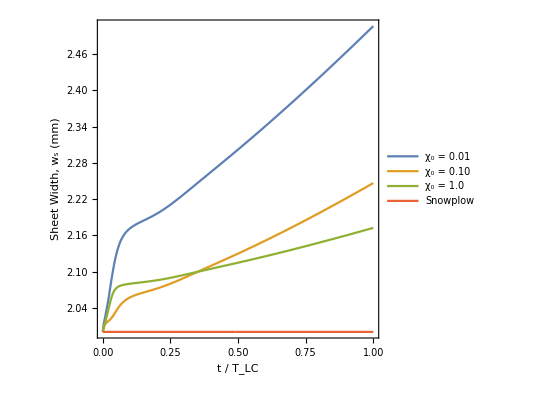

InterpolatingFunction::dmval: Input value {1.81524×10^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

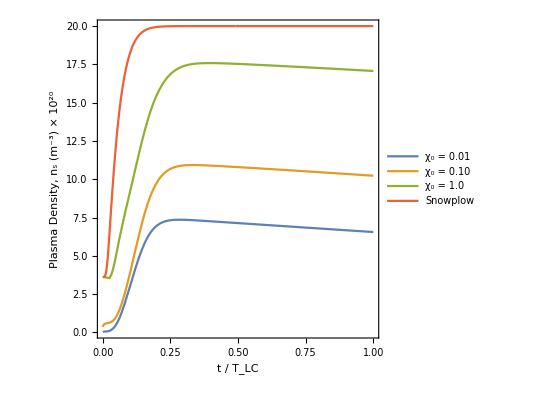

InterpolatingFunction::dmval: Input value {1.81524×10^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

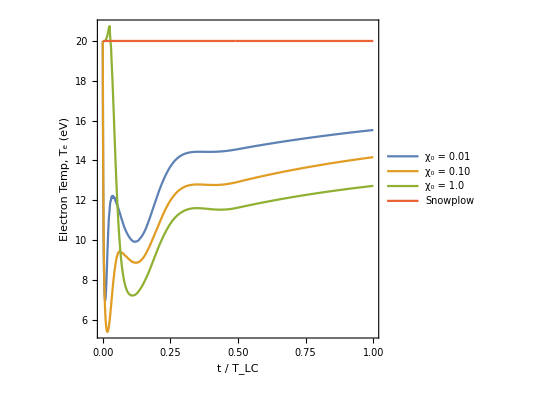

InterpolatingFunction::dmval: Input value {1.81524×10^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

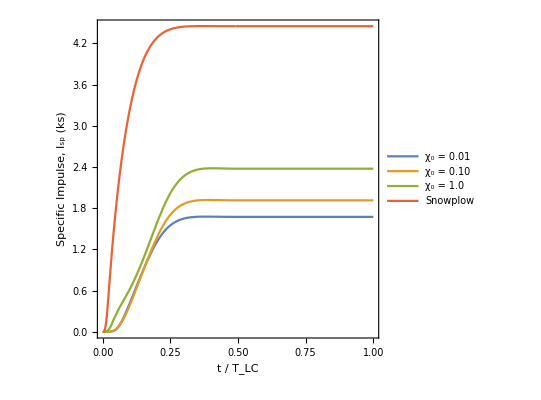

InterpolatingFunction::dmval: Input value {1.81524×10^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

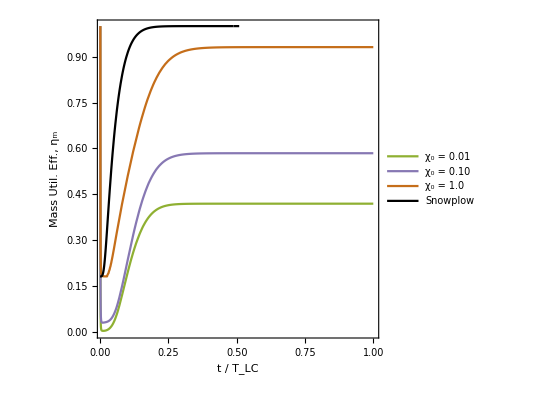

InterpolatingFunction::dmval: Input value {1.81524×10^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

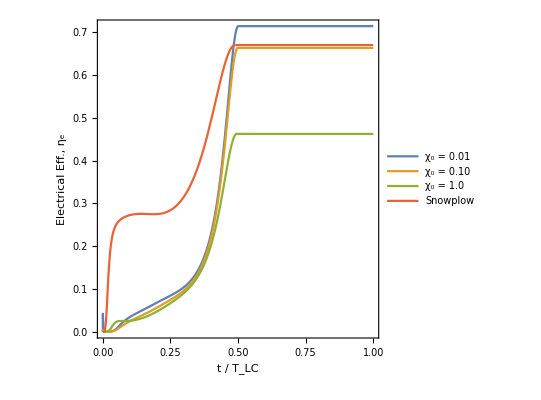

InterpolatingFunction::dmval: Input value {1.81524×10^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

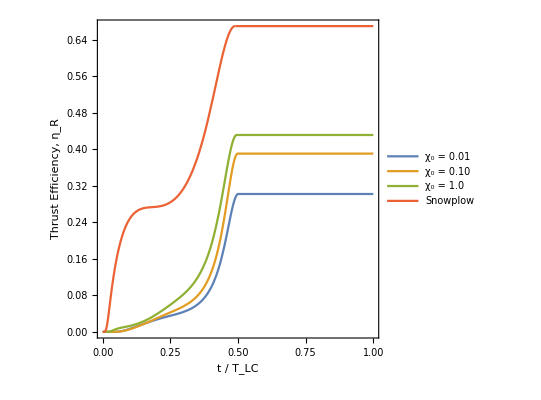

InterpolatingFunction::dmval: Input value {1.81524×10^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

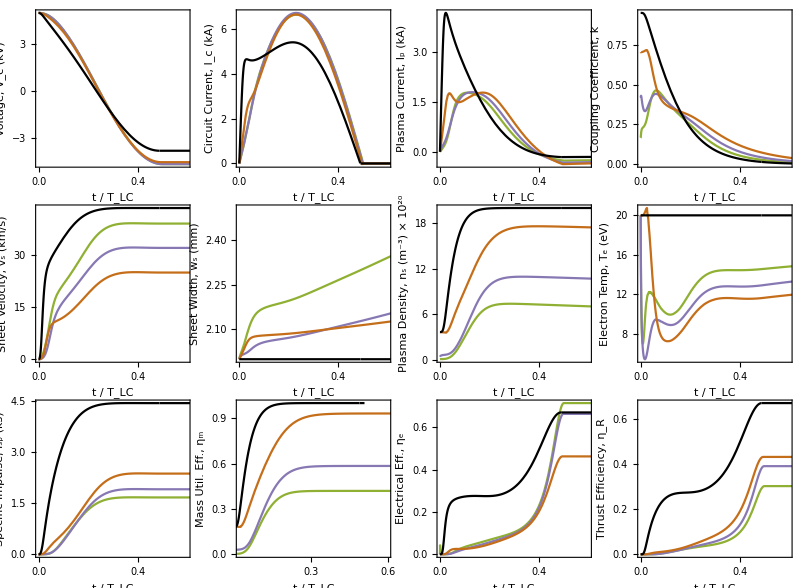

```mathematica
(** Adjust plot styles **)
PiPlot[Fun1_,Fun2_,Fun3_,Fun4_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale,Fun3[Τ τLC3]scale,Fun4[Τ τLC4]scale},{Τ,0,1},
PlotRange->{{0,1},All},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
PlotLegends->{"χ_0 = 0.01","χ_0 = 0.10","χ_0 = 1.0","Snowplow"}, (* Hard-coded for JAP 9/21 *)
Axes->False,
LabelStyle->{18,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
EffPiPlot[Fun1_,Fun2_,Fun3_,Fun4_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale,Fun3[Τ τLC3] scale,Fun4[Τ τLC4] scale},{Τ,0,1},
PlotRange->{{0.01,1},{0,1}},
PlotStyle->{ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[5]],ColorData[97,"ColorList"][[6]],Black},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
PlotLegends->{"χ_0 = 0.01","χ_0 = 0.10","χ_0 = 1.0","Snowplow"}, (* Hard-coded for JAP 9/21 *)
Axes->False,
LabelStyle->{18,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
JPlot[Fun1_,Fun2_,Fun3_,Fun4_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale,Fun3[Τ τLC3]scale,Fun4[Τ τLC4]scale},{Τ,0,1},
PlotRange->{{0,0.6},All},
PlotStyle->{ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[5]],ColorData[97,"ColorList"][[6]],Black},
(* PlotStyle->{{DotDashed,Black},{Dashed,Black},{Dotted,Black},{Black}}, *)
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
JkPlot[Fun1_,Fun2_,Fun3_,Fun4_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]/Lct1 scale,Fun2[Τ τLC2]/Lct2 scale,Fun3[Τ τLC3]/Lct3 scale,Fun4[Τ τLC4]/Lct4 scale},{Τ,0,1},
PlotRange->{{0,0.6},All},
PlotStyle->{ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[5]],ColorData[97,"ColorList"][[6]],Black},
(* PlotStyle->{{DotDashed,Black},{Dashed,Black},{Dotted,Black},{Black}}, *)
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
EffJPlot[Fun1_,Fun2_,Fun3_,Fun4_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale,Fun3[Τ τLC3]scale,Fun4[Τ τLC4]scale},{Τ,0,1},
PlotRange->{{0.02,0.6},{0,1}},
PlotStyle->{ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[5]],ColorData[97,"ColorList"][[6]],Black},
(* PlotStyle->{{DotDashed,Black},{Dashed,Black},{Dotted,Black},{Black}}, *)
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];

(** Individual Plots **)
PiPlot[V1,V2,V3,V4,"Voltage, V_c (kV)",10^-3]
PiPlot[Ic1,Ic2,Ic3,Ic4,"Circuit Current, I_c (kA)",10^-3]
PiPlot[Ip1,Ip2,Ip3,Ip4,"Plasma Current, I_p (kA)",10^-3]
Plot[{M1[Τ τLC1]/Lct1,M2[Τ τLC2]/Lct2,M3[Τ τLC3]/Lct3,M4[Τ τLC4]/Lct4},{Τ,0,1},
PlotRange->{{0,1},All},
PlotStyle->{{DotDashed,Black},{Dashed,Black},{Dotted,Black},{Black}},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC","Coupling Coefficient, k"},
PlotLegends->{"χ_0 = 0.01","χ_0 = 0.10","χ_0 = 1.0","Snowplow"}, (* Hard-coded for JAP 9/21 *)
Axes->False,
LabelStyle->{18,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]
PiPlot[vs1,vs2,vs3,vs4,"Sheet Velocity, v_s (km/s)",10^-3]
PiPlot[ws1,ws2,ws3,ws4,"Sheet Width, w_s (mm)",10^3]
PiPlot[ns1,ns2,ns3,ns4,"Plasma Density, n_s (m^-3) × 10^20",10^-20]
PiPlot[Te1,Te2,Te3,Te4,"Electron Temp, T_e (eV)",1]
PiPlot[Isp1,Isp2,Isp3,Isp4,"Specific Impulse, I_sp (ks)",10^-3]
EffPiPlot[ηm1,ηm2,ηm3,ηm4,"Mass Util. Eff., η_m",1]
PiPlot[EnergyFrac1,EnergyFrac2,EnergyFrac3,EnergyFrac4,"Electrical Eff., η_e",1]
PiPlot[ηTrec1,ηTrec2,ηTrec3,ηTrec4,"Thrust Efficiency, η_R",1]

(** Journal Output **)
Print[GraphicsGrid[{
{JPlot[V1,V2,V3,V4,"Voltage, V_c (kV)",10^-3],JPlot[Ic1,Ic2,Ic3,Ic4,"Circuit Current, I_c (kA)",10^-3],JPlot[Ip1,Ip2,Ip3,Ip4,"Plasma Current, I_p (kA)",10^-3],JkPlot[M1,M2,M3,M4,"Coupling Coefficient, k",1]},
{JPlot[vs1,vs2,vs3,vs4,"Sheet Velocity, v_s (km/s)",10^-3],JPlot[ws1,ws2,ws3,ws4,"Sheet Width, w_s (mm)",10^3],JPlot[ns1,ns2,ns3,ns4,"Plasma Density, n_s (m^-3) × 10^20",10^-20],JPlot[Te1,Te2,Te3,Te4,"Electron Temp, T_e (eV)",1]},
{JPlot[Isp1,Isp2,Isp3,Isp4,"Specific Impulse, I_sp (ks)",10^-3],EffJPlot[ηm1,ηm2,ηm3,ηm4,"Mass Util. Eff., η_m",1],JPlot[EnergyFrac1,EnergyFrac2,EnergyFrac3,EnergyFrac4,"Electrical Eff., η_e",1],JPlot[ηTrec1,ηTrec2,ηTrec3,ηTrec4,"Thrust Efficiency, η_R",1]}},
Spacings->{5,-5}, ImageSize-> 800]];
```

## Energy/Loss Mode Comparisons for Varying Inductance

```mathematica
Rct=0.005;
Eohmic1=Interpolation[Table[{tt,NIntegrate[Rct Ic1[dt]^2,{dt,0,tt}]},{tt,0,tmaxt1,tmaxt1/20}]];
Eohmic2=Interpolation[Table[{tt,NIntegrate[Rct Ic2[dt]^2,{dt,0,tt}]},{tt,0,tmaxt2,tmaxt2/20}]];
Eohmic3=Interpolation[Table[{tt,NIntegrate[Rct Ic3[dt]^2,{dt,0,tt}]},{tt,0,tmaxt3,tmaxt3/20}]];
Eohmic4=Interpolation[Table[{tt,NIntegrate[Rct Ic4[dt]^2,{dt,0,tt}]},{tt,0,tmaxt4,tmaxt4/20}]];
```

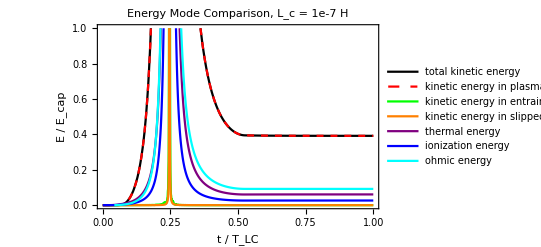

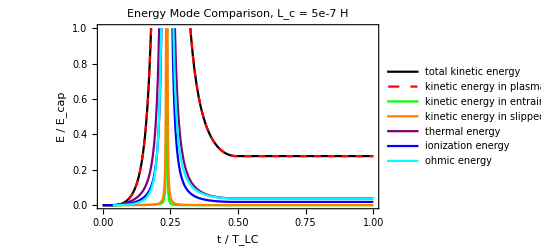

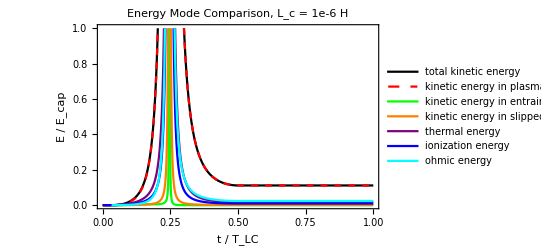

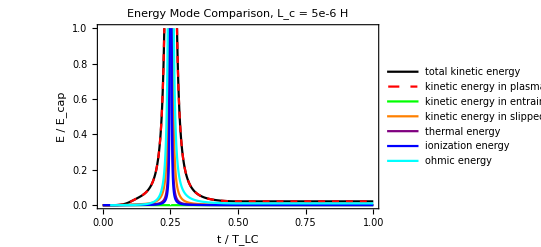

```mathematica
Print[Plot[{Eke1[Τ τLC1]/Ecap1[Τ τLC1],EkePl1[Τ τLC1]/Ecap1[Τ τLC1],EkeEnt1[Τ τLC1]/Ecap1[Τ τLC1],KEs1[Τ τLC1]/Ecap1[Τ τLC1],Ete1[Τ τLC1]/Ecap1[Τ τLC1],Ef1[Τ τLC1]/Ecap1[Τ τLC1],Eohmic1[Τ τLC1]/Ecap1[Τ τLC1]},{Τ,0,1},
PlotRange->{{0,1},{0,1}},
Frame->True,
ImageSize->400,
PlotLabel-> "Energy Mode Comparison, L_c = 1e-7 H",
FrameLabel->{"t / Τ_LC","E / E_cap"},
PlotLegends->{"total kinetic energy","kinetic energy in plasma","kinetic energy in entrained neutrals","kinetic energy in slipped neutrals","thermal energy","ionization energy","ohmic energy"},
PlotStyle->{{Thick,Black},{Dashed,Red},Green,Orange,Purple,Blue,Cyan},
Axes->False,
LabelStyle->{16,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]];
Print[Plot[{Eke2[Τ τLC2]/Ecap2[Τ τLC2],EkePl2[Τ τLC2]/Ecap2[Τ τLC2],EkeEnt2[Τ τLC2]/Ecap2[Τ τLC2],KEs2[Τ τLC2]/Ecap2[Τ τLC2],Ete2[Τ τLC2]/Ecap2[Τ τLC2],Ef2[Τ τLC2]/Ecap2[Τ τLC2],Eohmic2[Τ τLC2]/Ecap2[Τ τLC2]},{Τ,0,1},
PlotRange->{{0,1},{0,1}},
Frame->True,
ImageSize->400,
PlotLabel-> "Energy Mode Comparison, L_c = 5e-7 H",
FrameLabel->{"t / Τ_LC","E / E_cap"},
PlotLegends->{"total kinetic energy","kinetic energy in plasma","kinetic energy in entrained neutrals","kinetic energy in slipped neutrals","thermal energy","ionization energy","ohmic energy"},
PlotStyle->{{Thick,Black},{Dashed,Red},Green,Orange,Purple,Blue,Cyan},
Axes->False,
LabelStyle->{16,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]];
Print[Plot[{Eke3[Τ τLC3]/Ecap3[Τ τLC3],EkePl3[Τ τLC3]/Ecap3[Τ τLC3],EkeEnt3[Τ τLC3]/Ecap3[Τ τLC3],KEs3[Τ τLC3]/Ecap3[Τ τLC3],Ete3[Τ τLC3]/Ecap3[Τ τLC3],Ef3[Τ τLC3]/Ecap3[Τ τLC3],Eohmic3[Τ τLC3]/Ecap3[Τ τLC3]},{Τ,0,1},
PlotRange->{{0,1},{0,1}},
Frame->True,
ImageSize->400,
PlotLabel-> "Energy Mode Comparison, L_c = 1e-6 H",
FrameLabel->{"t / Τ_LC","E / E_cap"},
PlotLegends->{"total kinetic energy","kinetic energy in plasma","kinetic energy in entrained neutrals","kinetic energy in slipped neutrals","thermal energy","ionization energy","ohmic energy"},
PlotStyle->{{Thick,Black},{Dashed,Red},Green,Orange,Purple,Blue,Cyan},
Axes->False,
LabelStyle->{16,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]];
Print[Plot[{Eke4[Τ τLC4]/Ecap4[Τ τLC4],EkePl4[Τ τLC4]/Ecap4[Τ τLC4],EkeEnt4[Τ τLC4]/Ecap4[Τ τLC4],KEs4[Τ τLC4]/Ecap4[Τ τLC4],Ete4[Τ τLC4]/Ecap4[Τ τLC4],Ef4[Τ τLC4]/Ecap4[Τ τLC4],Eohmic4[Τ τLC4]/Ecap4[Τ τLC4]},{Τ,0,1},
PlotRange->{{0,1},{0,1}},
Frame->True,
ImageSize->400,
PlotLabel-> "Energy Mode Comparison, L_c = 5e-6 H",
FrameLabel->{"t / Τ_LC","E / E_cap"},
PlotLegends->{"total kinetic energy","kinetic energy in plasma","kinetic energy in entrained neutrals","kinetic energy in slipped neutrals","thermal energy","ionization energy","ohmic energy"},
PlotStyle->{{Thick,Black},{Dashed,Red},Green,Orange,Purple,Blue,Cyan},
Axes->False,
LabelStyle->{16,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]];
```

## EM and Mass Transparencies

General::munfl: Exp[-9.25066×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.2605×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7.13398×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

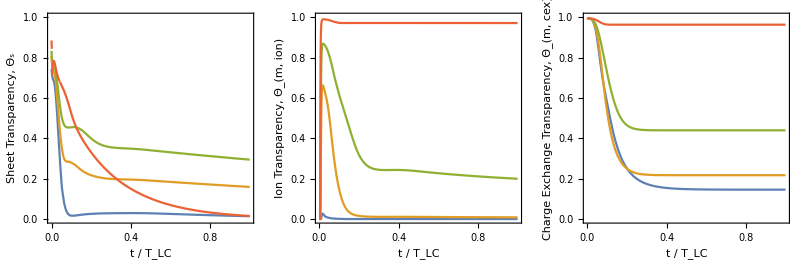

```mathematica
za=-0.002; 
Sion[Te_]:= 2.34 10^-14 Te^0.59 Exp[-17.44/Te]; (* Argon *)
σcx= 5 10^-19;
ec=1.6 10^-19;   
me=9.11 10^-31; 
kb=1.38 10^-23;  
g0=9.81; 
γ=5/3;  
μ0=4π 10^-7; 
ϵ0=8.85 10^-12;    
σen=4 10^-20;   (* Ar ion-neutral cross-section *)
Λ[ne_,Te_]:=Piecewise[{{23-Log[(ne 10^-6)^(1/2)Te^(-3/2)],Te<7.389},{24-Log[(ne 10^-6)^(1/2)Te^-1],Te≥7.389}}]    (* Coulomb Logarithm *)
νei[ne_,Te_]:=2.91 10^-12 ne Te^(-3/2)Λ[ne,Te]  (* e-i collision frequency *)
νen[nn_,Te_]:=nn σen ((8 ec Te)/(π me))^(1/2)    (*e-n collision frequency *)
ηcl[ne_,nn_,Te_]:=(me (νei[ne,Te]+νen[nn,Te]))/(ne ec^2)   (* Plasma Resistivity - Classical *)
δsd[Lterm_,Cp_,ne_,nn_,Te_]:=((2(ηcl[ne,nn,Te])(Lterm Cp)^(1/2))/μ0)^(1/2)   (* Skin Depth *)

δs1[t_]=δsd[L0t1+Lct1-M1[t]^2/Lct1,C0t1,ns1[t],nn1[zs1[t],t]+nf1[t],Te1[t]];
δs2[t_]=δsd[L0t2+Lct2-M2[t]^2/Lct2,C0t2,ns2[t],nn2[zs2[t],t]+nf2[t],Te2[t]];
δs3[t_]=δsd[L0t3+Lct3-M3[t]^2/Lct3,C0t3,ns3[t],nn3[zs3[t],t]+nf3[t],Te3[t]];
δs4[t_]=δsd[L0t4+Lct4-M4[t]^2/Lct4,C0t4,ns4[t],UnitStep[t-zs4[t]]nn4[zs4[t],t]+nf4[t],Te4[t]];

Θs1[t_]=Exp[-3ws1[t]/δs1[t]];
Θs2[t_]=Exp[-3ws2[t]/δs2[t]];
Θs3[t_]=Exp[-3ws3[t]/δs3[t]];
Θs4[t_]=Exp[-3ws4[t]/δs4[t]];
(* Θs1[t_]=1-M1[t]/Lct1 Exp[(zs1[t]-za)/zct1];
Θs2[t_]=1-M2[t]/Lct2 Exp[(zs2[t]-za)/zct2];
Θs3[t_]=1-M3[t]/Lct3 Exp[(zs3[t]-za)/zct3];
Θs4[t_]=1-M4[t]/Lct4 Exp[(zs4[t]-za)/zct4]; *)

Θmion1[t_]=Exp[(-ns1[t]ws1[t]Sion[Te1[t]])/vs1[t]];
Θmion2[t_]=Exp[(-ns2[t]ws2[t]Sion[Te2[t]])/vs2[t]];
Θmion3[t_]=Exp[(-ns3[t]ws3[t]Sion[Te3[t]])/vs3[t]];
Θmion4[t_]=Exp[(-ns4[t]ws4[t]Sion[Te4[t]])/vs4[t]];

Θmcex1[t_]=Exp[-ns1[t] ws1[t]σcx];
Θmcex2[t_]=Exp[-ns2[t] ws2[t]σcx];
Θmcex3[t_]=Exp[-ns3[t] ws3[t]σcx];
Θmcex4[t_]=Exp[-ns4[t] ws4[t]σcx];

(** Journal Output **)
JPlot[Fun1_,Fun2_,Fun3_,Fun4_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale,Fun3[Τ τLC3]scale,Fun4[Τ τLC4]scale},{Τ,0,1},
PlotRange->{{0,1},{0,1}},
(* PlotStyle->{ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[5]],ColorData[97,"ColorList"][[6]],Black}, *)
(* PlotStyle->{{DotDashed,Black},{Dashed,Black},{Dotted,Black},{Black}}, *)
(* PlotLegends->{"L_c = 1.0 × 10^-7 H","L_c = 5.0 × 10^-7 H","L_c = 1.0 × 10^-6 H","L_c = 5.0 × 10^-6 H"}, *)
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];

Print[GraphicsGrid[{
{JPlot[Θs1,Θs2,Θs3,Θs4,"Sheet Transparency, Θ_s",1],
JPlot[Θmion1,Θmion2,Θmion3,Θmion4,"Ion Transparency, Θ_(m, ion)",1],
JPlot[Θmcex1,Θmcex2,Θmcex3,Θmcex4,"Charge Exchange Transparency, Θ_(m, cex)",1]}},
Spacings->{5,-5}, ImageSize-> 800]];
```

## Journal Paper Formatting, Inductance Comparison, Rev 2

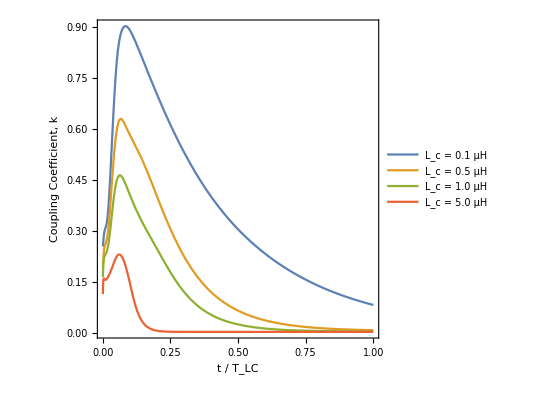

General::munfl: Exp[-9.25066×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.2605×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7.13398×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

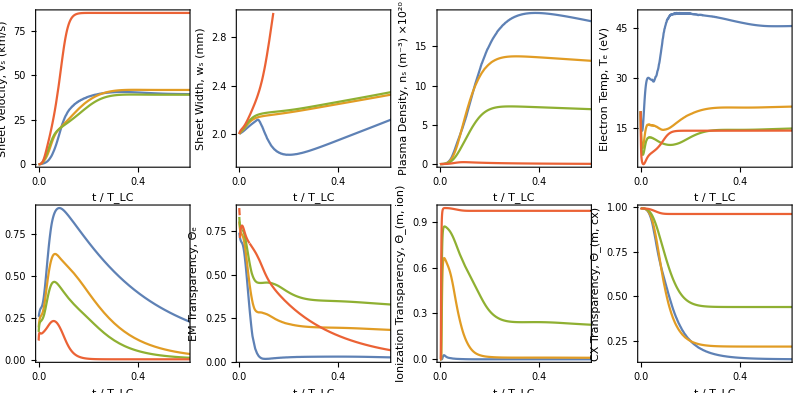

```mathematica
(** Adjust plot styles **)
JPlot[Fun1_,Fun2_,Fun3_,Fun4_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale,Fun3[Τ τLC3]scale,Fun4[Τ τLC4]scale},{Τ,0,1},
PlotRange->{{0,0.6},All},
(* PlotStyle->{{DotDashed,Black},{Dashed,Black},{Dotted,Black},{Black}}, *)
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
JkPlot[Fun1_,Fun2_,Fun3_,Fun4_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]/Lct1 scale,Fun2[Τ τLC2]/Lct2 scale,Fun3[Τ τLC3]/Lct3 scale,Fun4[Τ τLC4]/Lct4 scale},{Τ,0,1},
PlotRange->{{0,0.6},All},
(* PlotStyle->{{DotDashed,Black},{Dashed,Black},{Dotted,Black},{Black}}, *)
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
JwsPlot[Fun1_,Fun2_,Fun3_,Fun4_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1] scale,Fun2[Τ τLC2] scale,Fun3[Τ τLC3] scale,Fun4[Τ τLC4] scale},{Τ,0,1},
PlotRange->{{0,0.6},{1.75,3.0}},
(* PlotStyle->{{DotDashed,Black},{Dashed,Black},{Dotted,Black},{Black}}, *)
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
EffJPlot[Fun1_,Fun2_,Fun3_,Fun4_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale,Fun3[Τ τLC3]scale,Fun4[Τ τLC4]scale},{Τ,0,1},
PlotRange->{{0.02,0.6},{0,1}},
(* PlotStyle->{{DotDashed,Black},{Dashed,Black},{Dotted,Black},{Black}}, *)
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];

(** Transparency Calculations **)
za=-0.002; 
Sion[Te_]:= 2.34 10^-14 Te^0.59 Exp[-17.44/Te]; (* Argon *)
σcx= 5 10^-19;
ec=1.6 10^-19;   
me=9.11 10^-31; 
kb=1.38 10^-23;  
g0=9.81; 
γ=5/3;  
μ0=4π 10^-7; 
ϵ0=8.85 10^-12;    
σen=4 10^-20;   (* Ar ion-neutral cross-section *)
Λ[ne_,Te_]:=Piecewise[{{23-Log[(ne 10^-6)^(1/2)Te^(-3/2)],Te<7.389},{24-Log[(ne 10^-6)^(1/2)Te^-1],Te≥7.389}}]    (* Coulomb Logarithm *)
νei[ne_,Te_]:=2.91 10^-12 ne Te^(-3/2)Λ[ne,Te]  (* e-i collision frequency *)
νen[nn_,Te_]:=nn σen ((8 ec Te)/(π me))^(1/2)    (*e-n collision frequency *)
ηcl[ne_,nn_,Te_]:=(me (νei[ne,Te]+νen[nn,Te]))/(ne ec^2)   (* Plasma Resistivity - Classical *)
δsd[Lterm_,Cp_,ne_,nn_,Te_]:=((2(ηcl[ne,nn,Te])(Lterm Cp)^(1/2))/μ0)^(1/2)   (* Skin Depth *)

δs1[t_]=δsd[L0t1+Lct1-M1[t]^2/Lct1,C0t1,ns1[t],nn1[zs1[t],t]+nf1[t],Te1[t]];
δs2[t_]=δsd[L0t2+Lct2-M2[t]^2/Lct2,C0t2,ns2[t],nn2[zs2[t],t]+nf2[t],Te2[t]];
δs3[t_]=δsd[L0t3+Lct3-M3[t]^2/Lct3,C0t3,ns3[t],nn3[zs3[t],t]+nf3[t],Te3[t]];
δs4[t_]=δsd[L0t4+Lct4-M4[t]^2/Lct4,C0t4,ns4[t],UnitStep[t-zs4[t]]nn4[zs4[t],t]+nf4[t],Te4[t]];

Θs1[t_]=Exp[-3ws1[t]/δs1[t]];
Θs2[t_]=Exp[-3ws2[t]/δs2[t]];
Θs3[t_]=Exp[-3ws3[t]/δs3[t]];
Θs4[t_]=Exp[-3ws4[t]/δs4[t]];

Θmion1[t_]=Exp[(-ns1[t]ws1[t]Sion[Te1[t]])/vs1[t]];
Θmion2[t_]=Exp[(-ns2[t]ws2[t]Sion[Te2[t]])/vs2[t]];
Θmion3[t_]=Exp[(-ns3[t]ws3[t]Sion[Te3[t]])/vs3[t]];
Θmion4[t_]=Exp[(-ns4[t]ws4[t]Sion[Te4[t]])/vs4[t]];

Θmcex1[t_]=Exp[-ns1[t] ws1[t]σcx];
Θmcex2[t_]=Exp[-ns2[t] ws2[t]σcx];
Θmcex3[t_]=Exp[-ns3[t] ws3[t]σcx];
Θmcex4[t_]=Exp[-ns4[t] ws4[t]σcx];

(** Legend Generator **)
Plot[{M1[Τ τLC1]/Lct1,M2[Τ τLC2]/Lct2,M3[Τ τLC3]/Lct3,M4[Τ τLC4]/Lct4},{Τ,0,1},
PlotRange->{{0,1},All},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC","Coupling Coefficient, k"},
PlotLegends->{"L_c = 0.1 μH","L_c = 0.5 µH","L_c = 1.0 μH","L_c = 5.0 μH"}, (* Hard-coded for JAP 9/21 *)
Axes->False,
LabelStyle->{18,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]

(** Journal Output **)
Print[GraphicsGrid[{
{JPlot[vs1,vs2,vs3,vs4,"Sheet Velocity, v_s (km/s)",10^-3],JwsPlot[ws1,ws2,ws3,ws4,"Sheet Width, w_s (mm)",10^3],JPlot[ns1,ns2,ns3,ns4,"Plasma Density, n_s (m^-3) ×10^20",10^-20],JPlot[Te1,Te2,Te3,Te4,"Electron Temp, T_e (eV)",1]},
{JkPlot[M1,M2,M3,M4,"Coupling Coefficient, k",1],JPlot[Θs1,Θs2,Θs3,Θs4,"EM Transparency, Θ_e",1],JPlot[Θmion1,Θmion2,Θmion3,Θmion4,"Ionization Transparency, Θ_(m, ion)",1],JPlot[Θmcex1,Θmcex2,Θmcex3,Θmcex4,"CX Transparency, Θ_(m, cx)",1]}},
Spacings->{5,-5}, ImageSize-> 800]];
```

## Journal Paper Formatting, Snowplow Comparison, Rev 3

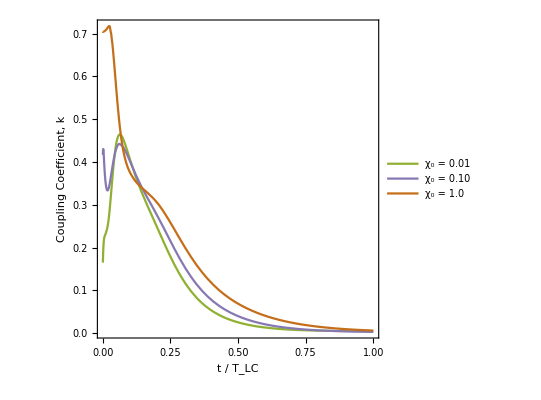

InterpolatingFunction::dmval: Input value {1.81524×10^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: Exp[-7.13398×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.56806×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.4299×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

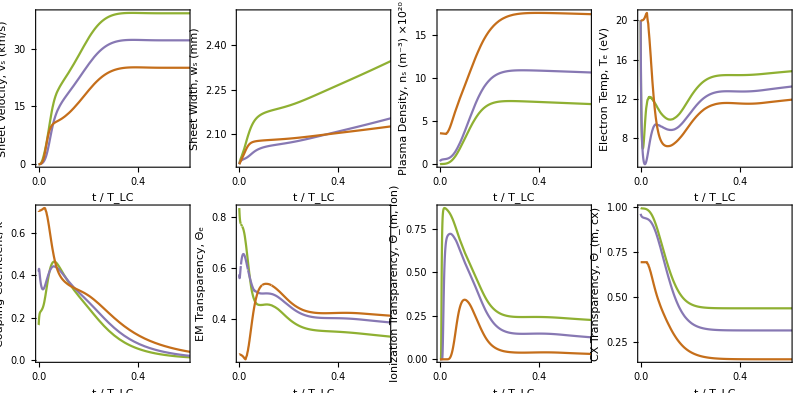

```mathematica
(** Adjust plot styles **)
JPlot[Fun1_,Fun2_,Fun3_,Fun4_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale,Fun3[Τ τLC3]scale,Fun4[Τ τLC4]scale},{Τ,0,1},
PlotRange->{{0,0.6},All},
PlotStyle->{ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[5]],ColorData[97,"ColorList"][[6]],{Dashed,Black}},
(* PlotStyle->{{DotDashed,Black},{Dashed,Black},{Dotted,Black},{Black}}, *)
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
JkPlot[Fun1_,Fun2_,Fun3_,Fun4_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]/Lct1 scale,Fun2[Τ τLC2]/Lct2 scale,Fun3[Τ τLC3]/Lct3 scale,Fun4[Τ τLC4]/Lct4 scale},{Τ,0,1},
PlotRange->{{0,0.6},All},
PlotStyle->{ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[5]],ColorData[97,"ColorList"][[6]],{Dashed,Black}},
(* PlotStyle->{{DotDashed,Black},{Dashed,Black},{Dotted,Black},{Black}}, *)
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
EffJPlot[Fun1_,Fun2_,Fun3_,Fun4_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale,Fun3[Τ τLC3]scale,Fun4[Τ τLC4]scale},{Τ,0,1},
PlotRange->{{0.02,0.6},{0,1}},
PlotStyle->{ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[5]],ColorData[97,"ColorList"][[6]],{Dashed,Black}},
(* PlotStyle->{{DotDashed,Black},{Dashed,Black},{Dotted,Black},{Black}}, *)
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];

(** Transparency Calculations **)
za=-0.002; 
Sion[Te_]:= 2.34 10^-14 Te^0.59 Exp[-17.44/Te]; (* Argon *)
σcx= 5 10^-19;
ec=1.6 10^-19;   
me=9.11 10^-31; 
kb=1.38 10^-23;  
g0=9.81; 
γ=5/3;  
μ0=4π 10^-7; 
ϵ0=8.85 10^-12;    
σen=4 10^-20;   (* Ar ion-neutral cross-section *)
Λ[ne_,Te_]:=Piecewise[{{23-Log[(ne 10^-6)^(1/2)Te^(-3/2)],Te<7.389},{24-Log[(ne 10^-6)^(1/2)Te^-1],Te≥7.389}}]    (* Coulomb Logarithm *)
νei[ne_,Te_]:=2.91 10^-12 ne Te^(-3/2)Λ[ne,Te]  (* e-i collision frequency *)
νen[nn_,Te_]:=nn σen ((8 ec Te)/(π me))^(1/2)    (*e-n collision frequency *)
ηcl[ne_,nn_,Te_]:=(me (νei[ne,Te]+νen[nn,Te]))/(ne ec^2)   (* Plasma Resistivity - Classical *)
δsd[Lterm_,Cp_,ne_,nn_,Te_]:=((2(ηcl[ne,nn,Te])(Lterm Cp)^(1/2))/μ0)^(1/2)   (* Skin Depth *)

δs1[t_]=δsd[L0t1+Lct1-M1[t]^2/Lct1,C0t1,ns1[t],nn1[zs1[t],t]+nf1[t],Te1[t]];
δs2[t_]=δsd[L0t2+Lct2-M2[t]^2/Lct2,C0t2,ns2[t],nn2[zs2[t],t]+nf2[t],Te2[t]];
δs3[t_]=δsd[L0t3+Lct3-M3[t]^2/Lct3,C0t3,ns3[t],nn3[zs3[t],t]+nf3[t],Te3[t]];
δs4[t_]=δsd[L0t4+Lct4-M4[t]^2/Lct4,C0t4,ns4[t],UnitStep[t-zs4[t]]nn4[zs4[t],t]+nf4[t],Te4[t]];

Θs1[t_]=Exp[-3ws1[t]/δs1[t]];
Θs2[t_]=Exp[-3ws2[t]/δs2[t]];
Θs3[t_]=Exp[-3ws3[t]/δs3[t]];
Θs4[t_]=Exp[-3ws4[t]/δs4[t]];

Θmion1[t_]=Exp[(-ns1[t]ws1[t]Sion[Te1[t]])/vs1[t]];
Θmion2[t_]=Exp[(-ns2[t]ws2[t]Sion[Te2[t]])/vs2[t]];
Θmion3[t_]=Exp[(-ns3[t]ws3[t]Sion[Te3[t]])/vs3[t]];
Θmion4[t_]=Exp[(-ns4[t]ws4[t]Sion[Te4[t]])/vs4[t]];

Θmcex1[t_]=Exp[-ns1[t] ws1[t]σcx];
Θmcex2[t_]=Exp[-ns2[t] ws2[t]σcx];
Θmcex3[t_]=Exp[-ns3[t] ws3[t]σcx];
Θmcex4[t_]=Exp[-ns4[t] ws4[t]σcx];

(** Individual Plot, Legend Generator **)
Plot[{M1[Τ τLC1]/Lct1,M2[Τ τLC2]/Lct2,M3[Τ τLC3]/Lct3,M4[Τ τLC4]/Lct4},{Τ,0,1},
PlotRange->{{0,1},All},
PlotStyle->{ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[5]],ColorData[97,"ColorList"][[6]],{Dashed,Black}},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC","Coupling Coefficient, k"},
PlotLegends->{"χ_0 = 0.01","χ_0 = 0.10","χ_0 = 1.0"}, (* Hard-coded for JAP 9/21 *)
Axes->False,
LabelStyle->{18,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]

(** Journal Output **)
Print[GraphicsGrid[{
{JPlot[vs1,vs2,vs3,vs4,"Sheet Velocity, v_s (km/s)",10^-3],JPlot[ws1,ws2,ws3,ws4,"Sheet Width, w_s (mm)",10^3],JPlot[ns1,ns2,ns3,ns4,"Plasma Density, n_s (m^-3) ×10^20",10^-20],JPlot[Te1,Te2,Te3,Te4,"Electron Temp, T_e (eV)",1]},
{JkPlot[M1,M2,M3,M4,"Coupling Coefficient, k",1],JPlot[Θs1,Θs2,Θs3,Θs4,"EM Transparency, Θ_e",1],JPlot[Θmion1,Θmion2,Θmion3,Θmion4,"Ionization Transparency, Θ_(m, ion)",1],JPlot[Θmcex1,Θmcex2,Θmcex3,Θmcex4,"CX Transparency, Θ_(m, cx)",1]}},
Spacings->{5,-5}, ImageSize-> 800]];
```